Last modified on: Tuesday, July 10, 2018 at 23:04

Author Info

Jiaying Xu

Kyle Keane

Smith College

Poster Session Content

The Past and Future of Occupations in the U.S.

Developments in artificial intelligence, genetics, robotics, nanotechnology, biotechnology, autonomous vehicles, to just name a few, are correlated with fundamental transformations of occupations and labor force in the US and will lay the foundation for a more comprehensive revolution in years to come. While the impending change holds great promise, the volatile patterns of the American job market also pose major challenges requiring proactive adaption by individuals, corporations and governments. It is thus essential to gain the ability to anticipate and prepare for future job content in a rapidly evolving employment landscape. This project makes an effort in becoming specific about the changes at hand--it examines the dynamics of workforces from 1850 to 2015 across industries and geographies. In particular, it explores the creation and displacement, benefits and burdens of each occupation, as well as the gender and age dynamics of changes underway.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

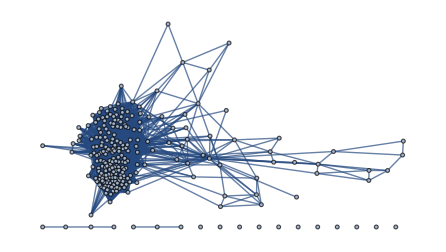

1. Greater job instability
Comparisons between jobs lost and jobs gained over the years reveal a rich mosaic of potential shifts in occupations in the years ahead, with important implications for workforce skills. Declining occupations tend to be physically and contextually predictable, including carpenter, athlete, baggageman, blacksmith, bookbinder, farmer, office machine operator, and motion picture picture projectionist, and physicist. Conversely, rising occupations include actor, artist, architect, author, baker, barber, bartender, bus driver, cook, decorator, designer, dentist and nutritionist. With rapid advances in automation and artificial intelligence, this result might imply that automation will have a lesser effect on jobs involving creating art, applying expertise, managing people, and social interactions.

2. Reduced Gender Gap 
Women’s labour force participation and economic power demonstrate an unambiguously positive trend in a somewhat turbulent landscape of technological and socioeconomic change. In the long run, the expansion of opportunities for women has the potential to transform the economies and societies of the U.S.. The continuing ascent of women in the workplace is also contributing to increasing diverse and dynamic workplace cultures.  Women are, on average, now participate more fully in professional and technical occupations than about 200 years ago, and the average prestigiousness of their positions are nearly the same as that of men. Nevertheless, industries like technology, energy, and infrastructure exemplify a particularly low overall female workforce participation. Conversely, industries that have a comparatively high proportion of women include household labor, Milliner, nurse, professor of physics, creditor, optometrist and Radio operator. 

3. Older Labor Force 
According to the data, workers over 40 show greater job engagement than younger workers over time. Factors for favoring older workers might be that their experience and skill subsets are increasingly valued, and that they exhibit greater professionalism with increased productivity. 

4. Nebulous Job Correlations
The strong correlations between Inmate and Economist, Apprentice Electrician and Professor of Statistics, Decorator and Nutritionist, and so on might have powerful implications for the underlying sociopolitical factors and market needs that have shaped and reshaped the job market. Yet, the high frequency of the occurrence of “Professor - Statistics” might suggest the embedded errors in the data collection itself.

1. Drivers of change, trends and disruptions. 
2. Skill sets of the future.
3. Change management and future workforce planning.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Landscape of Occupations from 1850 to 2015

Overview of the job market based on age, sex, and socioeconomic status.

Dataset[<>]

Employment trend by industry (e.g. Actor).

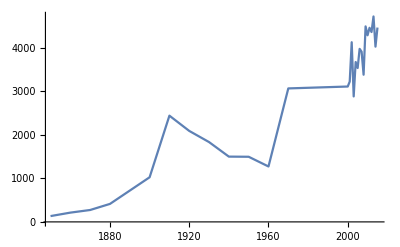

Employment trend by gender (e.g. professor).

-Graphics-

Employment trend by SEI.

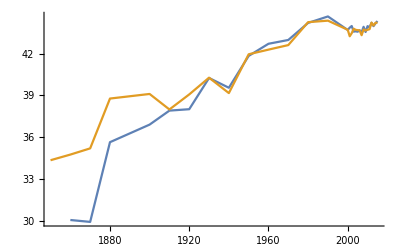

Changing popularity of occupations (1850 vs 2015).

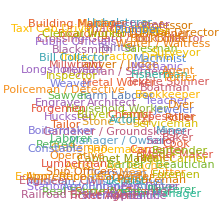
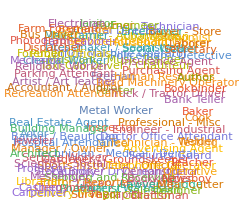

Occupational Correlations Over Time

Overall correlations among all occupations in dataset.

Dataset[<>]

Visualization of correlations among occupations.

-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

## I. Introduction

Developments in artificial intelligence, genetics, robotics, nanotechnology, biotechnology, autonomous vehicles, to just name a few, are correlated with fundamental transformations of occupations and labor force in the U.S. and will lay the foundation for a more comprehensive revolution in years to come. While the impending change holds great promise, the volatile patterns of the American job market also pose major challenges requiring proactive adaption by individuals, corporations and governments. It is thus essential to gain the ability to anticipate and prepare for future job content in a rapidly evolving employment landscape. This project makes an effort in becoming specific about the changes at hand--it examines the dynamics of workforces from 1850 to 2015 across industries and geographies. In particular, it explores the creation and displacement, benefits and burdens of each occupation, as well as the gender and age dynamics of changes underway. 

This dataset that forms the basis of this project is the result of an extensive survey of Census Bureau and Minnesota Population Center, representing more than 10 million employees across broad industry sectors in major developed and emerging economies. This analysis groups job functions into specific occupations and produces an overview of the job market based on age, sex, and socioeconomic status. Specific geographic considerations are intentionally omitted from this project. More attention is given to a set of broader socio-economic and demographic developments that each interacts in multiple directions and intensifies one another.

### 1. Dataset of Occupations from 1850 to 2015

This section creates a dataset of all occupations spanning from 1850 to 2015.

```mathematica
data=Import[First@FileNames["*.txt",NotebookDirectory[]],"TSV"];
(*import datas from a file*)
dataset=(Association@Thread[data[[1]]->data[[#]]])&/@Range[2,Length[data]]；
datasetD=Dataset@dataset;
datasetD
```

{<|year→1850 ； Null,sex→； Null,occupation→Accountant / Auditor ； Null,people→92.04 ； Null,age→10 ； Null,sei→72 ； Null|>,84535,<|year→2015 ； Null,sex→； Null,occupation→Welder ； Null,people→253. ； Null,age→90 ； Null,sei→24 ； Null|>}
 |  |  |  |

Dataset[<>]

### 2. Sample Overviews

This function builds association between years and corresponding number of occurrence for each occupation.

```mathematica
counts = AssociationMap[
Tally@Cases[data, {#, ___}][[All,3]] &, 
{1850,1860,1870,1880,1900,1910,1920,1930,1940,1950,1960,1970,1980,1990,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013, 2014, 2015}
]
```

<|1850→{{Accountant / Auditor,5},{Actor,3},{Agent,5},{Apprentice,4},{Apprentice - Carpenter,3},{Apprentice - Construction,1},{Architect,3},138,{Truck / Tractor Driver,7},{Typesetter,6},{Upholsterer,5},{Waiter / Waitress,5},{Weaver,8},{Welder,1}},28,2015→{1}|>
 |  |  |  |

#### 2.1. Sample Overview by Year and Number of Occupations

This section creates a histogram based on the association between year and number of occupations.

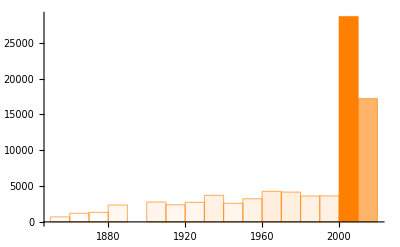

```mathematica
justData=Rest@data;
Histogram[justData[[All,1]],ColorFunction->Function[{height},Opacity[height]],ChartStyle->Orange]
```

#### 2.2. Sample Overview by Gender

This histogram compares the total labor force of each gender in the job market from 1850 to 2015. The left column represents the labor force of males and the right represents that of females.

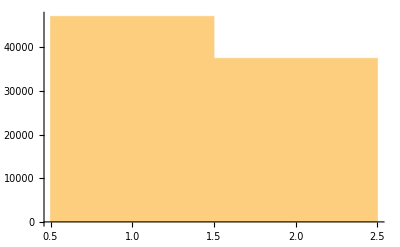

```mathematica
Histogram@justData[[All,2]]
```

#### 2.3. Sample Overview by Type of Occupations

This histogram compares the popularity of all occupations spanning from 1850 to 2015.

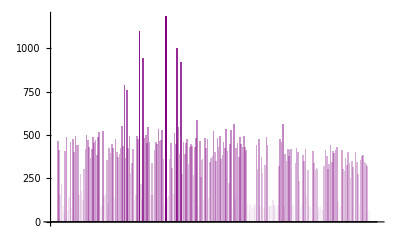

```mathematica
BarChart[Tally@justData[[All,3]],ColorFunction->Function[{height},Opacity[height]],ChartStyle->Purple]
```

### 3. Turbulent Landscape of Occupations from 1850 to 2015

This plot captures the rise and fall of all occupations from 1850 to 2015, showing the turbulent and volatile nature of the job market in the U.S..

```mathematica
headers = First[data];
points = Rest[data];
```

```mathematica
timeseries = GroupBy[
points, 
#[[3]] &,
TimeSeries[#[[All, 4]],{#[[All, 1]]}] &
];
```

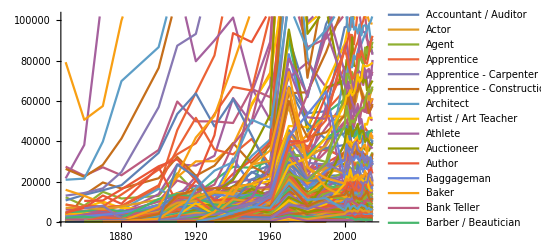

```mathematica
ListLinePlot[timeseries]
```

## II. Employment Trend

Discussions about employment trend have often been polarized between those foresee limitless opportunities in newly emerging job categories and those that foresee massive labour substitution and displacement of jobs. It is clear from the data in this project that while forecasts vary by industry, momentous change is underway. A more nuanced analysis is essential to determine the possible causes of displacement of workers or the emergence of new opportunities.

### 1. Employment Trend by Industry

This section provides a detailed overview of the trends and disruptions affecting each industry from 1850 to 2015. It also offers an aggregate summary of the relative outlook for all occupations in the years to come.

```mathematica
headers = First[data];
points = Rest[data];
timeseries = GroupBy[
points, 
#[[3]] &,
TimeSeries[#[[All, 4]],{#[[All, 1]]}] &
];
ListLinePlot/@timeseries
```

Comparisons between jobs lost and jobs gained over the years reveal a rich mosaic of potential shifts in occupations in the years ahead, with important implications for workforce skills. According to the graphs above, declining occupations include carpenter, athlete, baggageman, blacksmith, bookbinder, farmer, office machine operator, and motion picture picture projectionist, and physicist. Rising occupations include actor, artist, architect, author, baker, barber, bartender, bus driver, cook, decorator, designer, dentist and nutritionist. With rapid advances in automation and artificial intelligence, this result might imply that automation will have a lesser effect on jobs involving creating art, applying expertise, managing people, and social interactions.

### 2. Employment Trend by Gender

This section provides an overview of gender differences in access to each type of occupation.

```mathematica
genders = GroupBy[
MapAt[If[# ===1, "Male", "Female"]&, points, {All, 2}], 
{(*#[[1]] &,*)#[[3]] &, #[[2]] &},
 Map[Length, #]&
];
PieChart/@genders
```

The results confirm that most occupations are still dominated by men regardless of the time variation. In addition, women in the U.S. appear to be concentrated in low-productivity jobs and domestic activities. Of course, a focus exclusively on labor force participation provides only a partial picture of women’s and men’s experience in the labor market.

### 3. Employment Trend by Age

This section aims to show the age threshold for different types of occupations over time.

```mathematica
ages = GroupBy[
MapAt[Floor[#, 10]&, points, {All, 5}],
{#[[1]] &,#[[5]] &, #[[3]] &},
Map[Length, #, {2}]&
]
```

The result shows that child and elderly labors were not uncommon in late 1800s and early 1900s, and disappeared from the dataset in early 2000s. Overall, an increasing number of people are working into their later years, a trend that appears to continue.

### 4. Changing Socioeconomic Power of Males and Females

This section displays a comparison of the socioeconomic power between males and females from 1850 to 2015 by referring to the SEI, a measure of occupational status based upon the income level and educational attainment.

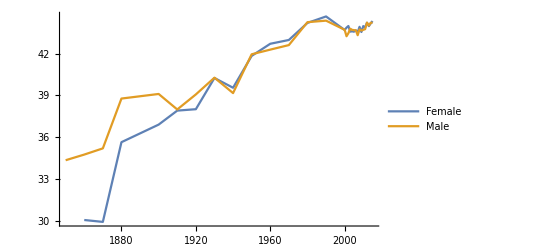

```mathematica
sie = GroupBy[
MapAt[If[# ===1, "Male", "Female"]&, points, {All, 2}],
{#[[2]] &, #[[1]] &},
Map[Mean, #[[All, All, 6]]]&
];
fmsie = ListLinePlot[sie]
```

The graph shows that females started with relatively low socioeconomic power in 1850, but maintained approximately the same level of power as males after around 1950. The fact that the lines converge before the Great Depression worth further exploration.

### 5. Changing Popularity of Occupations

In this section, the name of each occupation is sized according to its multiplicity in each designated year.

#### 5.1. 1850

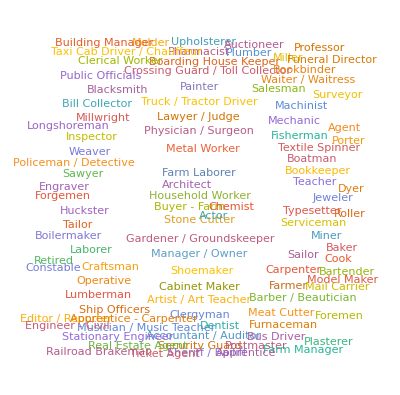

```mathematica
occ1850 = Select[data, #[[1]] == 1850 &][[All, 3]];
WordCloud[occ1850]
```

This graph shows that the most popular jobs in 1850 are farm laborer, metal worker, household worker and stone cutter.

#### 5.2. 1860

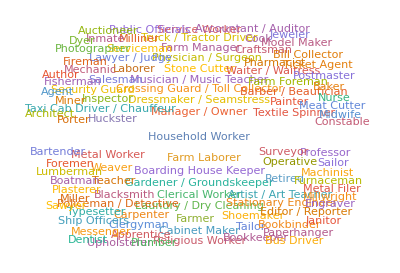

```mathematica
occ1860 = Select[data, #[[1]] == 1860 &][[All, 3]];
WordCloud[occ1860]
```

This graph shows that the most popular jobs in 1860 are household worker and farm laborer.

#### 5.3. 1990

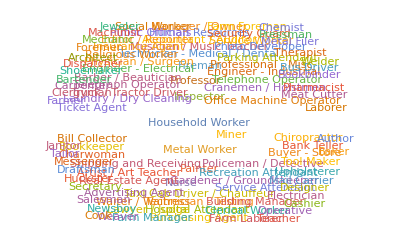

```mathematica
occ1990 = Select[data, #[[1]] == 1910 &][[All, 3]];
WordCloud[occ1990];
```

Surprisingly, the most popular job in 1990, household worker, is the same as that in 1860.

#### 5.4. 2015

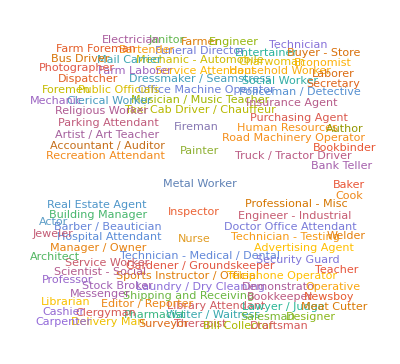

```mathematica
occ2015 = Select[data, #[[1]] == 2015 &][[All, 3]];
WordCloud[occ2015]
```

This graph shows that the most popular jobs in 2015 are metal worker, painter, inspector and nurse.

## III. Occupational Correlations Over Time

### 1. Visualization of Correlations

This section plots the possible correlations among different occupations from 1850 to 2015, showing whether any two jobs are related to one another or have similar patterns of rise and fall over time.

```mathematica
occupationPeople=Normal[datasetD[GroupBy["occupation"],GroupBy["year"],Total,"people"]];
```

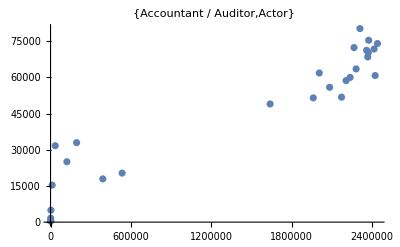
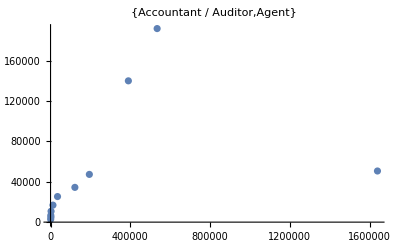
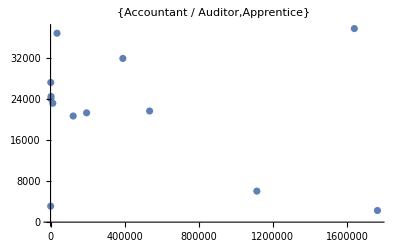
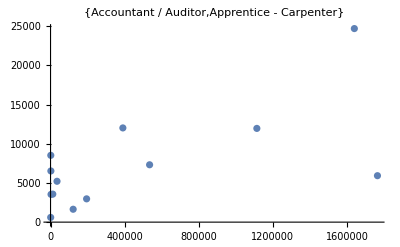
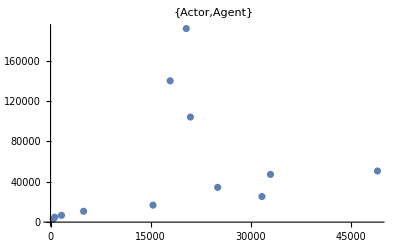
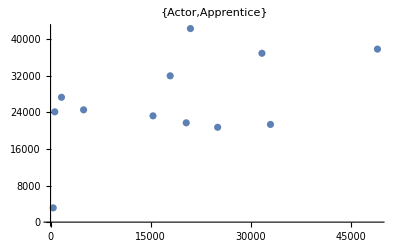
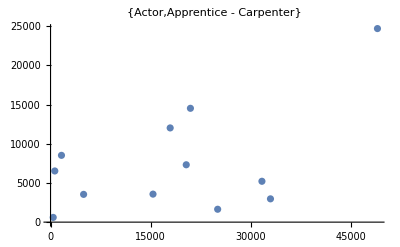
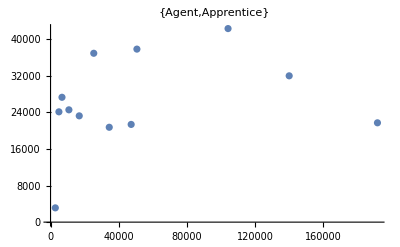

```mathematica
ListPlot[Values[Merge[KeyIntersection[Values[occupationPeople[[#]]]],Identity]],PlotLabel->#]&/@Subsets[Keys[occupationPeople][[1;;5]],{2}]
```

In the exemplary graphs above,  Accountant/Auditor and Actor show possible correlation, while the rest do not.

### 2. Correlations in Dataset

This section sorts out the degree of correlations among different occupations in a dataset.

```mathematica
occupationCorrelations=Association[#->Correlation@@Transpose[Values[Merge[KeyIntersection[Values[occupationPeople[[#]]]],Identity]]]&/@Subsets[Keys[occupationPeople],{2}]];
Dataset@Sort@occupationCorrelations
```

Dataset[<>]

The strong correlations between Inmate and Economist, Apprentice Electrician and Professor of Statistics, Decorator and Nutritionist, and so on might have powerful implications for the underlying sociopolitical factors and market needs that have shaped and reshaped the job market. Yet, the high frequency of the occurrence of “Professor - Statistics” might suggest the embedded errors in the data collection itself.

#### 3. Correlations in RelationGraph

This section visualizes the multi-relations among occupations from 1850 to 2015.

```mathematica
RelationGraph[occupationCorrelations[{#1,#2}]>0.9===True||occupationCorrelations[{#2,#1}]>0.9===True&,occupations(*,VertexLabels->"Name"*)]
```

## IV. Conclusions in Detail

1. Greater job instability
Comparisons between jobs lost and jobs gained over the years reveal a rich mosaic of potential shifts in occupations in the years ahead, with important implications for workforce skills. Declining occupations tend to be physically and contextually predictable, including carpenter, athlete, baggageman, blacksmith, bookbinder, farmer, office machine operator, and motion picture picture projectionist, and physicist. Conversely, rising occupations include actor, artist, architect, author, baker, barber, bartender, bus driver, cook, decorator, designer, dentist and nutritionist. With rapid advances in automation and artificial intelligence, this result might imply that automation will have a lesser effect on jobs involving creating art, applying expertise, managing people, and social interactions.

2. Reduced Gender Gap 
Women’s labour force participation and economic power demonstrate an unambiguously positive trend in a somewhat turbulent landscape of technological and socioeconomic change. In the long run, the expansion of opportunities for women has the potential to transform the economies and societies of the U.S.. The continuing ascent of women in the workplace is also contributing to increasing diverse and dynamic workplace cultures.  Women are, on average, now participate more fully in professional and technical occupations than about 200 years ago, and the average prestigiousness of their positions are nearly the same as that of men. Nevertheless, industries like technology, energy, and infrastructure exemplify a particularly low overall female workforce participation. Conversely, industries that have a comparatively high proportion of women include household labor, Milliner, nurse, professor of physics, creditor, optometrist and Radio operator. 

3. Older Labor Force 
According to the data, workers over 40 show greater job engagement than younger workers over time. Factors for favoring older workers might be that their experience and skill subsets are increasingly valued, and that they exhibit greater professionalism with increased productivity. 

4. Nebulous Job Correlations
The strong correlations between Inmate and Economist, Apprentice Electrician and Professor of Statistics, Decorator and Nutritionist, and so on might have powerful implications for the underlying sociopolitical factors and market needs that have shaped and reshaped the job market. Yet, the high frequency of the occurrence of “Professor - Statistics” might suggest the embedded errors in the data collection itself.

## V. Data Sources Links

1. IPUMS, “Integrated Occupation and Industry Codes and Occupational Standing Variables in the IPUMS.”
https://usa.ipums.org/usa/chapter4/chapter4.shtml
2. IPUMS, “Duncan Socioeconomic Index.” 
https://usa.ipums.org/usa-action/variables/SEI#codes_section

## VI. Future Directions

1. Drivers of change, trends and disruptions. 
2. Skill sets of the future.
3. Change management and future workforce planning.

## VII. Keywords

<history>

<occupation>

<future>

<gender>

<age>

<SEI>

## Project Summary

Developments in artificial intelligence, genetics, robotics, nanotechnology, biotechnology, autonomous vehicles, to just name a few, are correlated with fundamental transformations of occupations and labor force in the U.S. and will lay the foundation for a more comprehensive revolution in years to come. While the impending change holds great promise, the volatile patterns of the American job market also pose major challenges requiring proactive adaption by individuals, corporations and governments. It is thus essential to gain the ability to anticipate and prepare for future job content in a rapidly evolving employment landscape. This project makes an effort in becoming specific about the changes at hand--it examines the dynamics of workforces from 1850 to 2015 across industries and geographies. In particular, it explores the creation and displacement, benefits and burdens of each occupation, as well as the gender and age dynamics of changes underway. 
	This dataset that forms the basis of this project is the result of an extensive survey of Census Bureau and Minnesota Population Center, representing more than 10 million employees across broad industry sectors in major developed and emerging economies. This analysis groups job functions into specific occupations and produces an overview of the job market based on age, sex, and socioeconomic status. Specific geographic considerations are intentionally omitted from this project. More attention is given to a set of broader socio-economic and demographic developments that each interacts in multiple directions and intensifies one another.
	Overall, occupational growth are foreseeable in several sectors, generating a positive outlook for employment across many industries. However, the need for more human-based skills in certain job categories is highlighted by the high instability across most industries. Still, the technological developments need not become a race between machines and humans, but rather an opportunity for occupations to truly become a channel through which human beings can fully realize their potential. To realize this vision, more specific and up-to-date understanding of the changes underway is necessary to  lead individuals, businesses and governments through future transformations.